# Обучающий курс. Кластеризация данных

## Глава 1. Введение

1.1 Что такое кластеризация?

Кластеризация-это автоматическое разбиение элементов некоторого множества группы в зависимости от их схожести. Элементами множества может быть что угодно, например, данные или вектора характеристик. Сами же группы принято также называть кластерами.

## Кластеризация (пример 1)

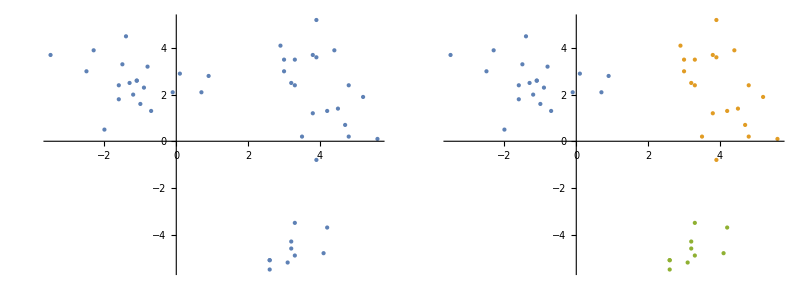

## Кластеризация (пример 2)

## Зачем это нужно?

У кластеризации существует большое количество практических применений как в информатике так и в других областях. Примерами применения могут служить:
1. Анализ данных
2. Извлечение и поиск информации
3. Группировка и распознавание объектов 
Так же кластеризация сама по себе является важной формой абстракции данных.
Кроме того, кластеризация является бурно развивающимся разделом современной теоретической информатики и в этой области можно получить ряд интересных исследовательских результатов.

## Формальные определения

Введем определения тех понятий, с которыми будем оперировать.
Объект - элементарная группа данных, с которой оперирует алгоритмы кластеризации.
Каждому объекту отождествляется вектор характеристик.
x= (х_1 ,...,х_d)
Компоненты х_i являются отдельными характеристиками объекта. Количество характеристик d определяет размерность пространства характеристик.
Множество, состоящее из всех векторов характеристик будем обозначать
æ.æ= (х_1, ...,х_n), где х_i = (x_(i,1), ...,х_(i,d))
Кластер - подмножество “близких друг к другу” объектов из æ.
Расстояние d(x_i,х_j) между объектами х_i и х_j -  результат применения выбранной метрики (или квази-метрики) в пространстве характеристик.

## Разница между кластеризацией и классификацией

Кластеризация разбивает множество объектов на группы, которые определяются только ее результатом. 
Классификация относит каждый объект к одной из заранее определенных групп.

1.2 Общая схема кластеризации

Кластеризация данных включает в себя следующие этапы :
1. Выделение характеристик
2. Определение метрики
3. Разбиение объектов на группы
4. Представление результатов

## Выделение вектора характеристик

Для начала необходимо выбрать свойства, которые характеризуют наши объекты. Ими могут быть количественные характеристики (координаты, интервалы ...), качественные характеристики (цвет, статус, воинское звание ...) и т.д.
Затем стоит попробовать уменьшить размерность пространства характеристических векторов, то есть выделить наиболее важные свойства объектов.Уменьшение размерности ускоряет процесс кластеризации и в ряде случаев позволяет визуально оценивать ее результаты. Выделенные характеристики стоит нормализовать. Далее все объекты представляются в виде характеристических векторов. Мы будем полностью отождествлять объект с его характеристическим вектором.

## Выбор метрики

Следующим этапом кластеризации является выбор метрики, по которой мы будем определять близость объектов.
Метрика выбирается в зависимости от : 
1. пространства, в котором расположены объекты
2. неявных характеристик кластеров
Например, если все координаты объекта непрерывны и вещественны, а кластеры должны представлять собой нечто вроде гиперсфер, то используется классическая метрика Евклида (на самом деле, чаще всего так и есть) :
d_2 (x_i, x_j) = (∑_(k=1)^d (x_(i,k)-x_(j,k))^2)^(1/2)=||x_i- x_j(||)_2

## Глава 2. Алгоритмы кластеризации

2.1 Алгоритмы кластеризации

1. Иерархические алгоритмы
2. k - means алгоритм
3. Минимальное покрывающее дерево
4. Метод ближайшего соседа
5. Алгоритмы нечеткой кластеризации
6. Применение нейронных сетей
7. Генетические алгоритмы
8. Метод закалки

## Классификация алгоритмов

Алгоритмы кластеризации делят на :
 • Строящие "снизу - вверх" и "сверху - вниз"
• Монотетические и политетические
• Непересекающиеся и нечеткие
• Детерминированные и стохастические
• Потоковые (online) и не потоковые
• Зависящие и не зависящие от начального разбиения
• Зависящие и не зависящие от порядка рассмотрения объектов

-Graphics-

2.2 Иерархические алгоритмы

Результатом работы иерархических алгоритмов является дендограмма (иерархия), позволяющая разбить исходное множество объектов на любое число кластеров.
Два наиболее популярных алгоритма, оба строят разбиение “снизу вверх”:
1. Single-link - на каждом шаге объединяет два кластера с наименьшим расстоянием между двумя любыми представителями 
2. Complete-link - на каждом шаге объединяет два кластера с наименьшим расстоянием между двумя наиболее удаленными представителями

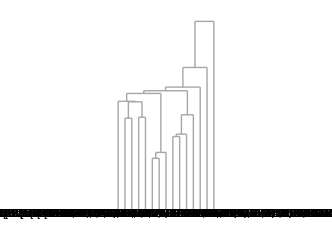
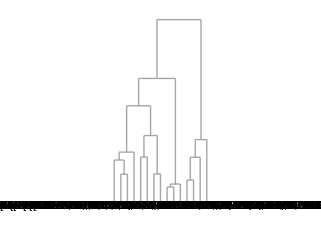
single-link | complete-link
-Graphics- | -Graphics-

2.3 k-Means алгоритм

Данный алгоритм состоит из следующих шагов : 
1. Случайно выбрать k точек, являющихся начальными "центрами масс" кластеров (любые k из n объектов, или вообще k случайных точек)
2. Отнести каждый объект к кластеру с ближайшим "центром масс"
3. Пересчитать "центры масс" кластеров согласно текущему членству
4. Если критерий остановки алгоритма не  удовлетворен, вернуться к шагу 2
В качестве критерия остановки обычно выбирают одни из двух :
1. Отсутствие перехода объектов из кластера в кластер на шаге 2
2.Минимальное изменение среднеквадратичной ошибки

*Алгоритм чувствителен к начальному выбору "центров масс"

## K - Means алгоритм пример :

## Реализация :

```mathematica
Clear[nearest]

nearest[centM_,x_]:={Nearest[centM,x]⟦1⟧,x}
ClearAll@fkm

fkm[data_,k_]:=Module[{centerOfMass=RandomSample[data,k],res1,res2,dat=data},
res1=nearest[centerOfMass,#]&/@dat;
res2=(Transpose/@(GatherBy[res1,First]))⟦All,2⟧]/;Depth@data==3
fkm[data_,k_]:=Module[{centerOfMass,res1,res2,dat=Flatten[data,1]},
centerOfMass=Mean/@data;
res1=nearest[centerOfMass,#]&/@dat;
res2=(Transpose/@(GatherBy[res1,First]))⟦All,2⟧]/;Depth@data==4
ClearAll@myFindClusters
myFindClusters[data_,k_]:=FixedPoint[fkm[#,k]&,data]
Manipulate[
ListPlot[myFindClusters[{{-14,14},{1,6},{0,1},{5,-11},{11,7},{10,4},{0,-15},{10,8},{13,7},{8,-10},{7,-10},{-9,-15},{-15,0},{-2,-7},{-12,8},{3,5},{14,8},{-2,2},{-3,9},{15,-5},{7,-5},{-6,-11},{13,11},{-14,2},{6,3},{-12,-12},{-2,-12},{5,-10},{0,0},{3,10}},i],PlotStyle-> PointSize[Large]],{{i,2,"Кол-во кластеров"},{1,2,3,4,5}}, ControlType->Setter]
```

2.4 Минимальное покрывающее дерево

Данный метод производит иерархическую кластеризацию "сверху - вниз".
Сначала все объекты помещаются в один кластер. Затем на каждом шаге один из кластеров разбивается на два, так чтобы расстояние между ними было максимальным.

## Пример :

## Реализация :

```mathematica
Clear[metodmpd];
metodmpd[list_]:=Module[{a=Permutations[list,{2}],e, s={},s1={}}, e=EuclideanDistance@@@a;Do[If[EuclideanDistance[list⟦i⟧,Flatten[a⟦FirstPosition[e,Max[e]],1⟧]]<EuclideanDistance[list⟦i⟧,Flatten[a⟦FirstPosition[e,Max[e]],2⟧]], AppendTo[s,list⟦i⟧],AppendTo[s1,list⟦i⟧]],{i,Length[list]}];{s, s1}]
Clear[mpd];
mpd[l_,k_]:=Module[{m=metodmpd[l], y=metodmpd[l], i={}},If[k>=2,Do[Do[AppendTo[i,Max[EuclideanDistance@@@Permutations[m⟦o⟧,{2}]]],{o, Length[m]}]; y=Delete[m,Position[i,Max[i]]⟦1,1⟧];AppendTo[y,metodmpd[m⟦Position[i,Max[i]]⟦1,1⟧⟧]⟦1⟧]; AppendTo[y,metodmpd[m⟦Position[i,Max[i]]⟦1,1⟧⟧]⟦2⟧];m=y;i= {},{u, k-2}]]; y]
Manipulate[ListPlot[mpd[{{-14,14},{1,6},{0,1},{5,-11},{11,7},{10,4},{0,-15},{10,8},{13,7},{8,-10},{7,-10},{-9,-15},{-15,0},{-2,7},{-12,8},{3,5},{14,8},{-2,2},{-3,9},{15,-5},{12,-5},{-6,-11},{13,11},{-14,2},{6,3},{-14,-1},{-12,12},{-2,-12},{5,-10},{0,0},{3,10}},i],PlotStyle->PointSize[Large]],{{i,2,"Шаг алгоритма"},{2,3,4,5,6,7,8}}, ControlType->Setter]
```

2.5 Метод ближайшего соседа

Множество методов иерархического кластерного анализа различается не только используемыми мерами сходства и различия, но и алгоритмами классификации. Из них наиболее распространен метод ближайшего соседа. Этот метод известен также под названием метод одиночной связи.
Пусть требуется провести классификацию заданного множества объектов методом ближайшего соседа. Расстояние между двумя классами определяется как расстояние между ближайшими их представителями.
Перед началом работы алгоритма рассчитывается матрица расстояний между объектами. На каждом шаге в матрице расстояний ищется минимальное значение, соответствующее расстоянию между двумя наиболее близкими кластерами. Найденные кластеры объединяются, образуя новый кластер. Эта процедура повторяется до тех пор, пока не будут объединены все кластеры.

## Алгоритм ближайшего соседа (пример):

## Реализация :

```mathematica
Clear[matr];
matr[sp_]:=(Table[If[m==n,1000,Min[Table[EuclideanDistance[sp⟦n,i⟧,sp⟦m,j⟧],{i , Length[sp⟦n⟧]},{j, Length[sp⟦m⟧]}]]] , {m,Length[sp]},{n,Length[sp]}]) 
Clear[mbsv];mbsv[sp_]:=Module[{sp1=sp,sp2, m , v={}},Do[ AppendTo[v,sp1];m =FirstPosition[matr[sp1],Min[matr[sp1]]];sp2= Delete[sp1,{{m⟦1⟧},{m⟦2⟧}}];AppendTo[sp2,sp1⟦m⟦1⟧⟧~Join~sp1⟦m⟦2⟧⟧]; sp1= sp2,{i,Length[sp]-1}];AppendTo[v,sp1] ]
Manipulate[ListPlot[mbsv[{{{-14,14},{-12,8},{-3,9},{-14,2},{-15,0}},{{1,6},{3,5},{6,3},{3,10},{10,4},{-2,2},{0,1},{0,0}},{{10,8},{11,7},{13,7},{14,8},{13,11}},{{7,-5},{8,-10},{7,-10},{5,-10},{5,-11},{-2,-7},{-2,-12},{-6,-11},{0,-15},{-12,-12},{-9,-15}}}]⟦i⟧,PlotStyle->PointSize[Large]],{{i,1,"Шаг алгоритма"},{1,2,3,4}}]
```

## Глава 3. Заключение

В данной главе вам предлагается ответить на несколько вопросов по пройденному материалу
Ниже представлен программный модуль, иллюстрирующий нахождение кластеров в изображении с помощью K-means алгоритма.

Далее вам предлагается ответить на несколько практических вопросов.